```mathematica
Clear["Global`*"]
```

```mathematica
LaunchKernels[6]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local]}

# Basin plots of Hénon-Heiles

The Hénon-Heiles Hamiltonian is given by

```mathematica
V=1/2(x^2+y^2)+x^2 y-1/3 y^3;
"H=1/2(x'[t]^2+y'[t]^2)+1/2(x[t]^2+y[t]^2)+x[t]^2y[t]-1/3y[t]^3"
```

H=1/2(x'[t]^2+y'[t]^2)+1/2(x[t]^2+y[t]^2)+x[t]^2y[t]-1/3y[t]^3

This gives the following equations of motions

```mathematica
ddx=x''[t]==-(x[t]+2x[t]y[t])
ddy= y''[t]==-(y[t]+x[t]^2-y[t]^2)
```

x''[t]==-x[t]-2 x[t] y[t]

y''[t]==-x[t]^2-y[t]+y[t]^2

To solve the system, we need four initial conditions (x0,y0,xdot0,ydot0). With the energy constraint, the needed initial conditions are reduced to three. We further constrain our initial conditions by choosing it such that the initial shooting velocity is perpendicular to the line from the origin to (x0,y0). Hence, the initial conditions are completely determined by (x0,y0) (and of course the energy).
getInitialVelocity takes as inputs the (energy,x0,y0) and checks if it is energetically allowed or not. If it is, then it outputs the initial velocities (xdot0,ydot0). If it isn’t then it outputs False.

```mathematica
getInitialVelocity[en_,x0_,y0_]:=Block[{vsquared,theta,vx0,vy0,returnvalue,xangle,yangle},
vsquared=2en-x0^2-y0^2-2 x0^2 y0+2/3 y0^3;
xangle=x0; yangle=y0;
If[!(x0==0&&y0==0),
If[x0==0,xangle=0;yangle=Sign[y0]*1,
If[y0==0,xangle=Sign[x0]*1;yangle=0]
]
]; (* If one of the components is 0, in calculating the angle, we set the value of the other component to ±1 so that the output of ArcTan is exact *)
theta=ArcTan[xangle,yangle];
If[vsquared<0||(x0==0&&y0==0),returnvalue=False,
vx0=√(vsquared*Sin[theta]^2);
vy0=√(vsquared*Cos[theta]^2);
If[0<theta≤Pi/2,returnvalue={-vx0,vy0},
If[Pi/2<theta≤Pi,returnvalue={-vx0,-vy0},
If[-Pi<theta≤-Pi/2,returnvalue={vx0,-vy0},
If[-Pi/2<theta≤0,returnvalue={vx0,vy0}]
]
]
]
];
Return[returnvalue]
];
```

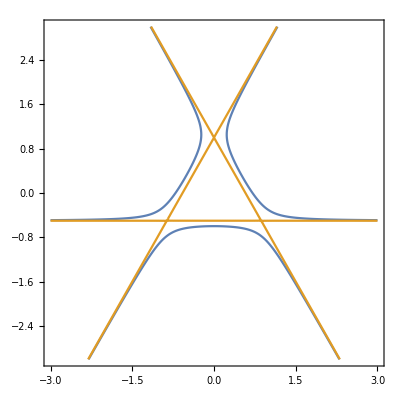

```mathematica
ContourPlot[{V==0.25,V==1/6},{x,-3,3},{y,-3,3},PlotPoints->100]
```

```mathematica
Plot3D[{V,0.25},{x,-2,2},{y,-2,2},ImageSize->500]
```

-Graphics3D-

The exits are defined as exit 1: y→∞; exit 2: y→-∞, x→-∞; exit 3: y→-∞, x→+∞

```mathematica
(* We define a particle to have exited when |y| > 100 *)
Attractors={WhenEvent[y[t]>50,Throw[1]],WhenEvent[y[t]<-50,If[x[t]<0,Throw[2],Throw[3]]],WhenEvent[t>MaximumT,Throw[4]]};
```

```mathematica
(* Checks to which exit a certain initial condition leads *)
CheckAttractor[en_,x0_,y0_]:=CheckAttractor[en,x0,y0]=Block[{velocity},
velocity=getInitialVelocity[en,x0,y0];
Catch[If[!velocity,Throw[0]];
NDSolve[{ddx,ddy,x[0]==x0,y[0]==y0,x'[0]==velocity⟦1⟧,y'[0]==velocity⟦2⟧}~Join~Attractors,{x,y},{t,0,MaximumT+1}];
]
];
```

We assign the corresponding colors of the basins

```mathematica
AttractorColors={0->White,1->Yellow,2->Blue,3->Red,4->Black}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0]}

```mathematica
SetSharedVariable[Progress];
```

## Energy = 0.25

```mathematica
MaximumT=10^5;pixels=1400;energy=0.25;Progress=0;
Region1y=Subdivide[1.2,-1.2,pixels];Region1x=Subdivide[-1.2,1.2,pixels];
```

```mathematica
Basin=Monitor[ParallelTable[Progress=Max[N@((Region1y⟦1⟧-y0)/(Region1y⟦1⟧-Region1y⟦-1⟧)),Progress];
CheckAttractor[energy,x0,y0],{y0,Region1y},{x0,Region1x},Method->"FinestGrained"],Progress];//AbsoluteTiming
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

{8493.78,Null}

```mathematica
MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{{{1,Region1y⟦1⟧},{pixels/2, "Y 0"},{pixels+1,Region1y⟦-1⟧}},{{1,Region1x⟦1⟧},{pixels/2, "X"},{pixels+1,Region1x⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Dynamics

```mathematica
Export["HenonbasinE"<>ToString[energy]<>"("<>ToString[pixels]<>"p).mx",Basin]
```

HenonbasinE0.25(1400p).mx

## Energy = 0.27

```mathematica
MaximumT=10^5;pixels=1400;energy=0.27;Progress=0;
Region1y=Subdivide[1.2,-1.2,pixels];Region1x=Subdivide[-1.2,1.2,pixels];
```

```mathematica
Basin=Monitor[ParallelTable[Progress=Max[N@((Region1y⟦1⟧-y0)/(Region1y⟦1⟧-Region1y⟦-1⟧)),Progress];
CheckAttractor[energy,x0,y0],{y0,Region1y},{x0,Region1x},Method->"FinestGrained"],Progress];//AbsoluteTiming
```

ArcTan::indet: Indeterminate expression ArcTan[0.,0.] encountered.

{8368.84,Null}

```mathematica
MatrixPlot[Basin,ColorRules->AttractorColors,FrameTicks->{{{1,Region1y⟦1⟧},{pixels/2, "Y 0"},{pixels+1,Region1y⟦-1⟧}},{{1,Region1x⟦1⟧},{pixels/2, "X"},{pixels+1,Region1x⟦-1⟧}}},ImageSize->500,BaseStyle->{FontSize->24},LabelStyle->{FontSize->24}]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["HenonbasinE"<>ToString[energy]<>"("<>ToString[pixels]<>"p).mx",Basin]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Dynamics\Henon-Heiles

HenonbasinE0.27(1400p).mx